## Graph convert function (graphToNet)

graphToNet[graph, ini] takes a graph (Mathematica style) and returns a list of elements {m_j,{n_(j 1),n_(j 2),…,n_(j N_j)}}; with j∈{1,…, N} (N the number of nodes in the graph), n_(j s) the s-th neighbour of node j. 
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini_List]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

## Lights at the edges, all nodes donate per tick, packages change node according to some probability

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ Each tick t, a number of marbles m_t≈p M shift position from one node to another, here 0≤p≤1, and M=∑_(j=1)^N m_j is the initial number of marbles

netEvolve[graph,ω,ϕ,T,p] takes a graph (represented as previously described), with N nodes, an integer T, and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,0]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
marbles[[-1]]+out
];
Do[
AppendTo[marbles,add[remove[graph]]];
t++;
,{i,T}
];
marbles
];
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,1]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph],tochoosefrom=Range[Length[graph]],newdist},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
marbles[[-1]]+out
];
Do[
(*shuffle marbles around*)
newdist=RandomChoice[tochoosefrom,n];
newdist=add[remove[graph]]-ConstantArray[1,n]+(Count[newdist,#]&/@tochoosefrom);
AppendTo[marbles,newdist];
t++;
,{i,T}
];
marbles
];
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,p_/;0<p<1]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph],tochoosefrom=Range[Length[graph]],goingout,newones},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
marbles[[-1]]+out
];
Do[
(*shuffle marbles around*)
goingout=(#>p&/@RandomReal[{0,1},n])/.{True->1,False->0};
newones=RandomChoice[tochoosefrom,Total[goingout]];
newones=Count[newones,#]&/@tochoosefrom;
AppendTo[marbles,add[remove[graph]]-goingout+newones];
t++;
,{i,T}
];
marbles];
```

## Lights at the edges, all nodes donate per tick

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays.

netEvolve[graph,ω,ϕ,T] takes a graph (represented as previously described), with N nodes, an integer T, and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going*)
remove[g_]:=Module[{ret=ConstantArray[0,Length[g]],i,out},
For[i=1,i≤Length[g],i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
ret
];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
(*Print[out];*)
marbles[[-1]]+out
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,{i,T}
];
marbles
]
```

### Test

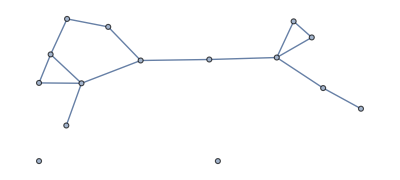

```mathematica
gr=RandomGraph[{15,15}]
```

```mathematica
test=graphToNet[gr,{15,1}]
```

{{15,{4,11}},{0,{9,15}},{0,{5,12}},{0,{1,9}},{0,{3,7,12,14}},{0,{}},{0,{5,10}},{0,{15}},{0,{2,4,15}},{0,{7}},{0,{1,14,15}},{0,{3,5}},{0,{}},{0,{5,11}},{0,{2,8,9,11}}}

```mathematica
ω=Table[RandomChoice[{0,π,2π}],{i,15},{j,15}];
ϕ=Table[RandomChoice[{0,π,2π}],{i,15},{j,15}];
ω[[1,4]]=0;
marbles=netEvolve[test,ω,ϕ,500];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 1):

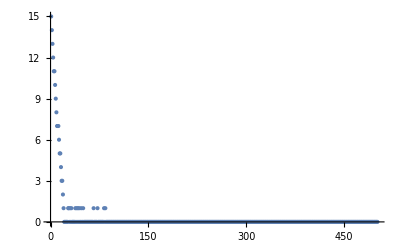

```mathematica
ListPlot[marbles[[All,1]],PlotRange->All]
```

El 12, que está solo, permanece constante

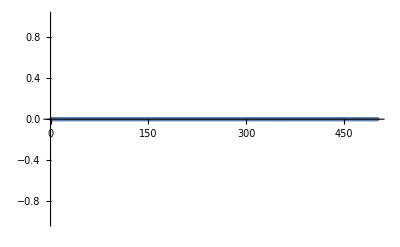

```mathematica
ListPlot[marbles[[All,-3]]]
```

El número total de pelotas por tick es

```mathematica
Total/@marbles//Short
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,«475»,15,15,15,15,15,15,15,15,15,15,15,15,15}

La densidad por nodos en un tick (el 15)

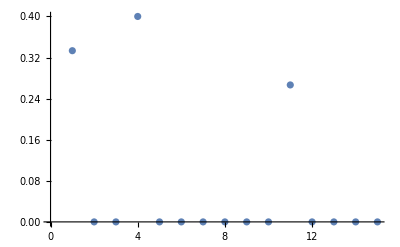

```mathematica
ListPlot[marbles[[15]]/Total[marbles[[-1]]]]
```

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-

### Triangle

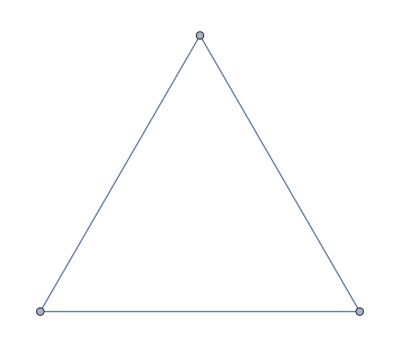

```mathematica
gr=AdjacencyGraph[{{0,1,1},{1,0,1},{1,1,0}}]
```

```mathematica
triangle=graphToNet[gr,{100,1}]
```

{{100,{2,3}},{0,{1,3}},{0,{1,2}}}

#### No lights

```mathematica
ω=Table[0,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[triangle,ω,ϕ,45000];
```

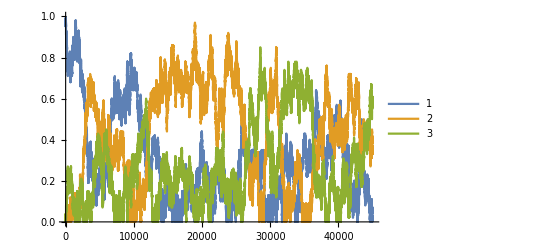

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

#### Lights

```mathematica
Manipulate[ListLinePlot[Table[Sin[w t],{t,30}]],{w,0,2π,π/10}]
```

```mathematica
ω=Table[π/10,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[triangle,ω,ϕ,25000];
```

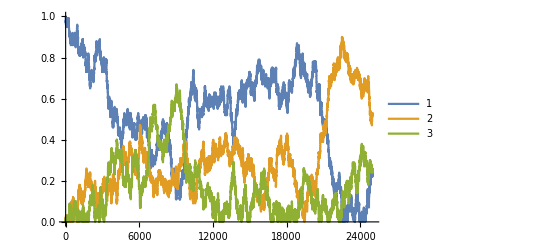

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

### Line

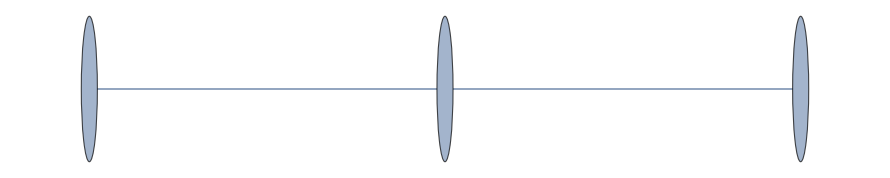

```mathematica
gr=AdjacencyGraph[{{0,1,0},{1,0,1},{0,1,0}}]
```

```mathematica
line=graphToNet[gr,{100,1}]
```

{{100,{2}},{0,{1,3}},{0,{2}}}

#### No lights

```mathematica
ω=Table[0,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[line,ω,ϕ,15000];
```

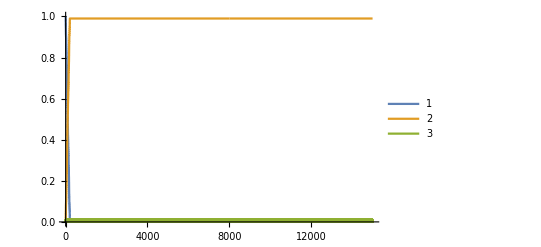

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

#### Lights

```mathematica
Manipulate[ListLinePlot[Table[Sin[w t],{t,30}]],{w,0,2π,π/10}]
```

```mathematica
ω=Table[π/10,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[line,ω,ϕ,5000];
```

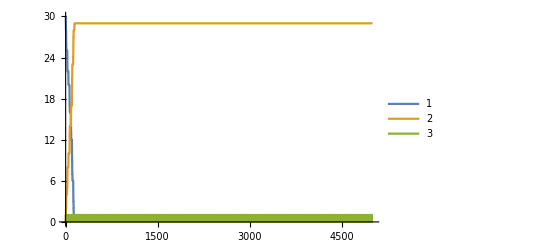

```mathematica
ListLinePlot[marbles//Transpose,PlotLegends->{"1","2","3"}]
```

## Lights at the nodes, all nodes donate per tick

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j},ω_j,ϕ_j}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m; and ω_j,ϕ_j the frecuency and phase that determines if marbles are able to leave the node or not. When ω_j==0 or Sin[ω_j t+ϕ_j]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_j==0∨Sin[ω_j t+ϕ_i]≥ 0, otherwise the marble stays.

graphToNet[graph, ini,ω,ϕ] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,…,n_(1 N_1)},ω_1,ϕ_1},…,{m_j,{n_(j 1),n_(j 2),…,n_(j N_j)},ω_j,ϕ_j},…,{m_N,{n_(N 1),n_(N 2),…,n_(N N_j)},ω_N,ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j,  and ω_j and ϕ_j determined by ω and ϕ respectively. 
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles
ω can be:
	• a number (then ω_i→ω ∀ i∈{1,2,…,N}
	• a list of lenght N, then ω_i→ω[[i]]
ϕ can be:
	• a number (then ϕ_i→ϕ ∀ i∈{1,2,…,N}
	• a list of lenght N, then ϕ_i→ϕ[[i]]

```mathematica
graphToNet[g_Graph,ini:{a_,n_},ω_?NumericQ,ϕ_?NumericQ]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#,ω,ϕ}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini:{a_,p_},ω_?VectorQ,ϕ_?NumericQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[Transpose[{ConstantArray[0,n],nei,ω,ConstantArray[ϕ,n]}],{p,1}->a]
]/;Length[ω]==VertexCount[g];
graphToNet[g_Graph,ini:{a_,p_},ω_?NumericQ,ϕ_?VectorQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[Transpose[{ConstantArray[0,n],nei,ConstantArray[ω,n],ϕ}],{p,1}->a]
]/;Length[ϕ]==VertexCount[g];
graphToNet[g_Graph,ini:{a_,p_},ω_?VectorQ,ϕ_?VectorQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[Transpose[{ConstantArray[0,n],nei,ω,ϕ}],{p,1}->a]
]/;Length[ϕ]==Length[ω]==VertexCount[g];
graphToNet[g_Graph,ini_List,ω_?NumericQ,ϕ_?NumericQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,ConstantArray[ω,n],ConstantArray[ϕ,n]}]
]/;Length[ini]==VertexCount[g];
graphToNet[g_Graph,ini_List,ω_?VectorQ,ϕ_?NumericQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,ω,ConstantArray[ϕ,n]}]
]/;Length[ini]==Length[ϕ]==VertexCount[g];
graphToNet[g_Graph,ini_List,ω_?NumericQ,ϕ_?VectorQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,ConstantArray[ω,n],ϕ}]
]/;Length[ini]==Length[ϕ]==VertexCount[g];
graphToNet[g_Graph,ini_List,ω_?VectorQ,ϕ_?NumericQ]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,ω,ϕ}]
]/;Length[ini]==Length[ω]==Length[ϕ]==VertexCount[g];
```

netEvolve[graph,T] takes a graph (represented as previously described), with N nodes, an integer T, and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

```mathematica
ω=1/2;
```

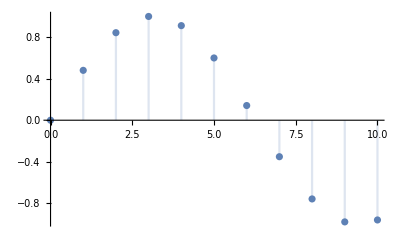

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

```mathematica
netEvolve[graph_List,T_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove maps over graph and returns 0 if no marbel can leaves the node or the number of the node where the marble is going*)
remove[{_,{},_,_}]:=0;
remove[{_,neighbors_List,ω_,ϕ_}]:=If[ω==0∨Sin[ω t+ϕ]>0,
RandomChoice[neighbors],0];
(*add takes the output from remove and builds the new marble distribution*)
add[inter_List]:=Module[{out=ConstantArray[0,n],i},
For[i=1,i≤Length[inter],i++,
If[inter[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[inter[[i]]]]=out[[inter[[i]]]]+1;,
0];
];
(*Print[out];*)
marbles[[-1]]+out
];
Do[
(*Print[remove/@graph];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove/@graph]];
t++;
(*Print[t]*)
,{i,T}
];
marbles
]
```

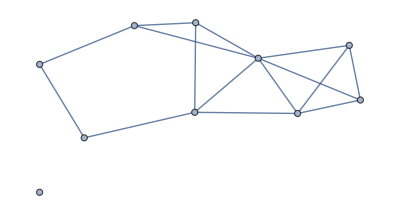

```mathematica
gr=RandomGraph[{10,15}]
```

```mathematica
test=graphToNet[gr,{10,1},0,0]
```

{{10,{2,5},0,0},{0,{1,4,8,10},0,0},{0,{4,5,10},0,0},{0,{2,3,6,7,8,10},0,0},{0,{1,3},0,0},{0,{4,7,8},0,0},{0,{4,6,8},0,0},{0,{2,4,6,7},0,0},{0,{},0,0},{0,{2,3,4},0,0}}

```mathematica
marbles=netEvolve[test,300];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 1):

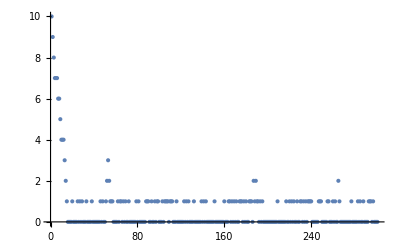

```mathematica
ListPlot[marbles[[All,1]],PlotRange->All]
```

El 9, que está solo, permanece constante

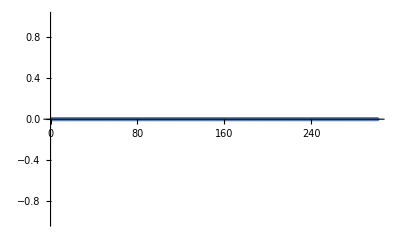

```mathematica
ListPlot[marbles[[All,9]]]
```

El número total de pelotas por tick es

```mathematica
Total/@marbles
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

La densidad de nodos en un tick (el último)

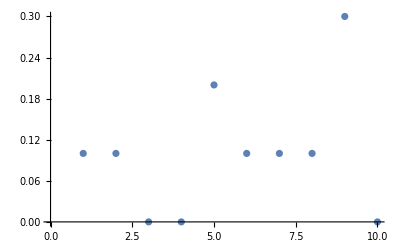

```mathematica
ListPlot[marbles[[-1]]/Total[marbles[[-1]]]]
```

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-

## Lights at the nodes

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j},ϕ_j}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m; and ϕ_j the phase that determines if marbles are able to leave the node or not. When ϕ_j==0 or Sin[ω t+ϕ_j]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ One node passes one of its marbles to one of its neighbors. 
	■ The marble is passed if ϕ_j==0∨Sin[ω t+ϕ_i]≥ 0, otherwise the marble stays. 
	■ The node is chosen based on the number of marbles it has (this is, if node’s A has more marbles than node B, it is more likely that the A is chosen).

graphToNet[graph, ini,fun] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,…,n_(1 N_1)},ϕ_1},…,{m_j,{n_(j 1),n_(j 2),…,n_(j N_j)},ϕ_j},…,{m_N,{n_(N 1),n_(N 2),…,n_(N N_j)},ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j  and ϕ_j determined by fun. 
By default fun is RandomChoice[{9/10,1/20,1/20}→{0,π,2π}], fun fills the phases ϕ_i. 
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles

```mathematica
graphToNet[g_Graph,ini:{a_,n_},ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#,ϕ[]}&/@nei,{n,1}->a]
]
```

```mathematica
graphToNet[g_Graph,ini_List,ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei,Table[ϕ[],{Length[ini]}]}]
]/;Length[ini]==VertexCount[g]
```

```mathematica
graphToNet[g_Graph,ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],n=VertexCount[g]},
{RandomInteger[n],#,ϕ[]}&/@nei
]
```

netEvolve[graph, ω,T] takes a graph (represented as previously described), with N nodes, an integer T, and a real ω and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

```mathematica
ω=1/2;
```

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

-Graphics-

```mathematica
netEvolve[graph_List,ω_Real?Positive,T_Integer]:=Module[
{marbles=graph[[All,1]],nodes=Range[Length[graph]],add,t=0},
add[marbles_List]:=Module[{out=RandomChoice[marbles->nodes],in},
t++;
(*Print[t];*)
If[graph[[out]][[-1]]==0∨Sin[ω t+graph[[out]][[-1]]]>0,
in=RandomChoice[graph[[out,2]]];
(*Print[{out,in}];*)
ReplacePart[marbles,{out->marbles[[out]]-1,in->marbles[[in]]+1}],
marbles
]
];
NestList[add,marbles,T]
]
```

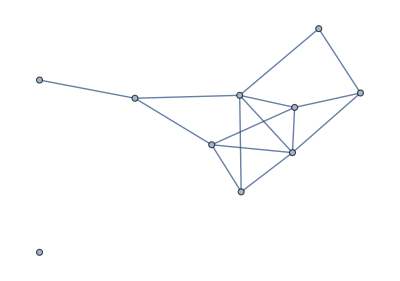

```mathematica
gr=RandomGraph[{10,15}]
```

```mathematica
test=graphToNet[gr,{10,1}]
```

{{10,{2,5,8},0},{0,{1,6,7,8,9},0},{0,{6,7,8},0},{0,{},0},{0,{1,7,8,9},0},{0,{2,3},0},{0,{2,3,5,8},0},{0,{1,2,3,5,7},0},{0,{2,5,10},0},{0,{9},0}}

```mathematica
marbles=netEvolve[test,.5,50];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 1):

```mathematica
marbles[[All,1]]
```

{10,9,8,7,6,5,4,3,3,3,3,3,3,3,4,3,3,2,2,2,2,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

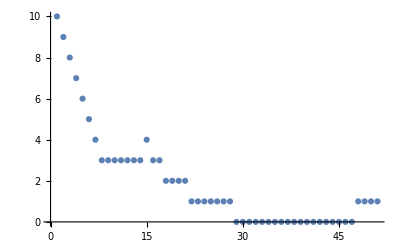

```mathematica
ListPlot[marbles[[All,1]]]
```

El 4, que está solo, permanece constante

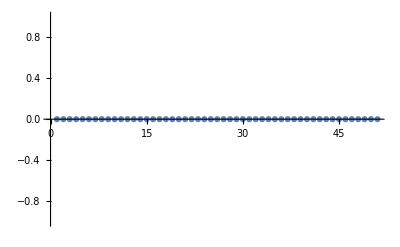

```mathematica
ListPlot[marbles[[All,4]]]
```

El número total de pelotas es

```mathematica
Total/@marbles
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

La densidad de nodos en un tick (el último)

```mathematica
ListPlot[marbles[[-1]]/Total[marbles[[-1]]]]
```

-Graphics-

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-

## Lights at the links

Given a graph with an initial configuration of marbles at each node, move one marble from one node to one of its neighbors accordinf to the following rules:
	• The origin node is selected according to how many marbles it has (this is, if node A has more marbles than node B, there is a higher chance of selecting node A).
	• Once the node is selected, check if Cos[ω_(i j) t_i+ϕ_(i j)]≥0, if this is the case move the marble, otherwise don’t do nothing. Here ω_(i j) and ϕ_(i j) are both positive real numbers.

evolve[graph, T, ω,ϕ, ini] takes a graph (graph) and implements the rules given above for T iterations.
	• ω can be a number, vector or a matrix of positive numbers.
		- if it is a number, then ω_(i j)→ω  ∀ i,j ∈{1,…,N} with N the number of nodes in graph.
		- if it is a vector, then ω_(i j)→ω[[i]]  ∀ i ∈{1,…,N} with N the number of nodes in graph.
		- if it is a matrix, then ω_(i j)→ω[[i,j]]
	• ϕ can be a positive number, vector or a matrix of positive numbers.
		- if it is a number, then ϕ_(i j)→ϕ  ∀ i,j ∈{1,…,N} with N the number of nodes in graph.
		- if it is a list, then ϕ_(i j)→ϕ[[i]]  ∀ i ∈{1,…,N} with N the number of nodes in graph.
		- if it is a matrix, then ϕ_(i j)→ϕ[[i,j]]
	• ini is optional, if given it must be a vector of N elements. This would be the initial marble population.

```mathematica
evolve[g_Graph,T_Integer,ω_?NumericQ,ϕ_?NumericQ,ini:{}]:=Module[
{numnodes=VertexCount[g],out,neighbors=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],nodes,add,t=1},
out=If[ini=={},ReplacePart[ConstantArray[0,numnodes],1->numnodes],ini];
nodes=Range[VertexCount[g]];
add[marbles_]:=Module[{pick=RandomChoice[marbles->nodes],in},
t++;
in=RandomChoice[neighbors[[pick]]];
If[Cos[ω t + ϕ]<0,
marbles,
ReplacePart[marbles,{pick->marbles[[pick]]-1,in->marbles[[in]]+1}]
]
];
NestList[add,out,T]
]
```

```mathematica
evolve[g_Graph,T_Integer,ω_?VectorQ,ϕ_?VectorQ,ini:{}]:=Module[
{numnodes=VertexCount[g],out,neighbors=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],nodes,add,t=1},
out=If[ini=={},ReplacePart[ConstantArray[0,numnodes],1->numnodes],ini];
nodes=Range[VertexCount[g]];
add[marbles_]:=Module[{pick=RandomChoice[marbles->nodes],in},
t++;
in=RandomChoice[neighbors[[pick]]];
If[Cos[ω[[pick]] t + ϕ[[pick]]]<0,
marbles,
ReplacePart[marbles,{pick->marbles[[pick]]-1,in->marbles[[in]]+1}]
]
];
NestList[add,out,T]
]
```

```mathematica
evolve[g_Graph,T_Integer,ω_?MatrixQ,ϕ_?MatrixQ,ini_:{}]:=Module[
{numnodes=VertexCount[g],out,neighbors=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],nodes,add,t=1},
out=If[ini=={},ReplacePart[ConstantArray[0,numnodes],1->numnodes],ini];
nodes=Range[VertexCount[g]];
add[marbles_]:=Module[{pick=RandomChoice[marbles->nodes],in},
t++;
in=RandomChoice[neighbors[[pick]]];
If[Cos[ω[[pick,in]] t + ϕ[[pick,in]]]<0,
marbles,
ReplacePart[marbles,{pick->marbles[[pick]]-1,in->marbles[[in]]+1}]
]
];
NestList[add,out,T]
]
```

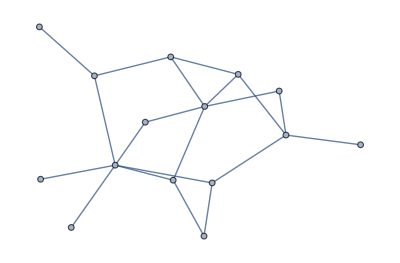

```mathematica
g=RandomGraph[{15,20}]
```

```mathematica
evolve[g,10,RandomReal[{0,20},{VertexCount[g],VertexCount[g]}],RandomReal[{0,2π},{VertexCount[g],VertexCount[g]}]]
```

{{15,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{14,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{13,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{13,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{12,0,1,0,2,0,0,0,0,0,0,0,0,0,0},{12,0,1,0,2,0,0,0,0,0,0,0,0,0,0},{11,0,1,0,3,0,0,0,0,0,0,0,0,0,0},{11,0,1,0,3,0,0,0,0,0,0,0,0,0,0},{11,0,1,1,2,0,0,0,0,0,0,0,0,0,0},{10,0,1,1,3,0,0,0,0,0,0,0,0,0,0}}

## Lights at the edges, all nodes donate per tick, nodes have a limited capacity

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ A marble is passed if the recieving node has enough space left to recieve all incoming marbles.

netEvolve[graph,ω,ϕ,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list of two lists {E,J} with E a M×T matrix where every row has the number of marbles  of its corresponding node for each tick (this is, element e_(m,t) is the number of marbles of node m at tick t); and J a list of T elements where j_t is the number of marbles that where moved within the network in tick t.
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

### Test

```mathematica
gr=RandomGraph[{15,15}]
```

-Graphics-

```mathematica
test=graphToNet[gr,{15,1}]
```

{{15,{4,11}},{0,{9,15}},{0,{5,12}},{0,{1,9}},{0,{3,7,12,14}},{0,{}},{0,{5,10}},{0,{15}},{0,{2,4,15}},{0,{7}},{0,{1,14,15}},{0,{3,5}},{0,{}},{0,{5,11}},{0,{2,8,9,11}}}

```mathematica
ω=Table[RandomChoice[{0,π,2π}],{i,15},{j,15}];
ϕ=Table[RandomChoice[{0,π,2π}],{i,15},{j,15}];
ω[[1,4]]=0;
marbles=netEvolve[test,ω,ϕ,500];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 1):

```mathematica
ListPlot[marbles[[All,1]],PlotRange->All]
```

-Graphics-

El 12, que está solo, permanece constante

```mathematica
ListPlot[marbles[[All,-3]]]
```

-Graphics-

El número total de pelotas por tick es

```mathematica
Total/@marbles//Short
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,«475»,15,15,15,15,15,15,15,15,15,15,15,15,15}

La densidad por nodos en un tick (el 15)

```mathematica
ListPlot[marbles[[15]]/Total[marbles[[-1]]]]
```

-Graphics-

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-

### Triangle

```mathematica
gr=AdjacencyGraph[{{0,1,1},{1,0,1},{1,1,0}}]
```

-Graphics-

```mathematica
triangle=graphToNet[gr,{100,1}]
```

{{100,{2,3}},{0,{1,3}},{0,{1,2}}}

#### No lights

```mathematica
ω=Table[0,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[triangle,ω,ϕ,45000];
```

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

-Graphics-

#### Lights

```mathematica
Manipulate[ListLinePlot[Table[Sin[w t],{t,30}]],{w,0,2π,π/10}]
```

```mathematica
ω=Table[π/10,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[triangle,ω,ϕ,25000];
```

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

-Graphics-

### Line

```mathematica
gr=AdjacencyGraph[{{0,1,0},{1,0,1},{0,1,0}}]
```

-Graphics-

```mathematica
line=graphToNet[gr,{100,1}]
```

{{100,{2}},{0,{1,3}},{0,{2}}}

#### No lights

```mathematica
ω=Table[0,{i,Length[triangle]},{j,Length[triangle]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[line,ω,ϕ,15000];
```

```mathematica
ListLinePlot[marbles/100//Transpose,PlotLegends->{"1","2","3"}]
```

-Graphics-

#### Lights

```mathematica
Manipulate[ListLinePlot[Table[Sin[w t],{t,30}]],{w,0,2π,π/10}]
```

```mathematica
ω=Table[π/10,{i,Length[line]},{j,Length[line]}];
ϕ=Table[0,{i,15},{j,15}];
marbles=netEvolve[line,ω,ϕ,5000];
```

```mathematica
ListLinePlot[marbles//Transpose,PlotLegends->{"1","2","3"}]
```

-Graphics-